## The Law of Motion

#### LoM1

```mathematica
SetParameters[<|"β"->1.5,"μ"->2,"λ"->1,"ρ"->0.9,"δ"->0.7|>];
ps = PowerStructure[NormalizeTernaryT[({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, 0, 0}})]];
reel = Part[Map[ShowPowerStructure[#,<|"circular"->True,"size"->{65,65}|>]&,SimulateLawOfMotion[ps]],{1,3,5,7}];
SpacedRow[MapIndexed[AddCaption[#,"t = "<>ToString[First[#2]]]&,reel],30]
```

-Graphics-
t = 1-Graphics-
t = 2-Graphics-
t = 3-Graphics-
t = 4

#### LoM hierarchy

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.95,"δ"->0.8|>];
ps = PowerStructure[NormalizeTernaryT[({{0, 1, 1, 1, 1}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}})]];
reel = Part[Map[ShowPowerStructure[#,<|"circular"->False,"size"->{75,40}|>]&,SimulateLawOfMotion[ps]],{1,3,5,7}];
SpacedRow[MapIndexed[AddCaption[#,"t = "<>ToString[First[#2]]]&,reel],25]
```

-Graphics-
t = 1-Graphics-
t = 2-Graphics-
t = 3-Graphics-
t = 4

#### LoM rebellion

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.95,"δ"->0.8|>];
ps = PowerStructure[{1.4,.8,.8,.8},NormalizeTernaryT[({{0, -1, -1, -1}, {-1, 0, 0, 0}, {-1, 0, 0, 0}, {-1, 0, 0, 0}})]];
reel = Part[Map[ShowPowerStructure[#,<|"circular"->False,"size"->{75,50}|>]&,SimulateLawOfMotion[ps]],{1,2,3,4}];
SpacedRow[MapIndexed[AddCaption[#,"t = "<>ToString[First[#2]]]&,reel],25]
```

-Graphics-
t = 1-Graphics-
t = 2-Graphics-
t = 3-Graphics-
t = 4

#### LoM bipolar

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.95,"δ"->0.8|>];
ps = PowerStructure[{2,.5,.5,2,1,.6,.7,1.2},NormalizeTernaryT[({{0, -1, -1, -1, 0, 0, 0, 1}, {-1, 0, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]];
reel = Part[Map[ShowPowerStructure[#,<|"circular"->True,"size"->{75,75}|>]&,SimulateLawOfMotion[ps]],{1,3,5,7}];
SpacedRow[MapIndexed[AddCaption[#,"t = "<>ToString[First[#2]]]&,reel],35]
```

-Graphics-
t = 1-Graphics-
t = 2-Graphics-
t = 3-Graphics-
t = 4

#### LoM animation 1

```mathematica
SetParameters[<|"β"->2.,"μ"->5.,"λ"->0.995,"α"->2.25,"δ"->0.6,"ρ"->0.9,"k"->9|>];
ExportSimulationAsGIF[SimulateLawOfMotion[<|"s"->{0.3576304433563648,0.366501095396554,0.35332749259091883,0.9999999999999999,0.6648617243479856,0.6163433495253299},"T"->{{0.9,0.024999999999999994,0.04999999999999999,0.,0.,0.033333333333333326},{0.033333333333333326,0.9,0.,0.09999999999999998,0.09999999999999998,-0.033333333333333326},{0.033333333333333326,0.,0.9,0.,0.,-0.033333333333333326},{0.,0.024999999999999994,0.,0.9,0.,0.},{0.,0.024999999999999994,0.,0.,0.9,0.},{0.033333333333333326,-0.024999999999999994,-0.04999999999999999,0.,0.,0.9}}|>],"/Users/mpoulshock/Documents/Github/QuantitativeRealism/Supplementary Materials/Wiki Images/Law of Motion/LoM animation 1.gif",<|"circular"->False|>];
```

#### LoM animation 2

```mathematica
SetParameters[<|"β"->2.,"μ"->5.,"λ"->0.995,"α"->2.25,"δ"->0.7,"ρ"->0.95,"k"->9|>];
ps = PowerStructure[{2,.5,.5,2,1,.6,.7,1.2},NormalizeTernaryT[({{0, -1, -1, -1, 0, 0, 0, 1}, {-1, 0, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]];
ExportSimulationAsGIF[SimulateLawOfMotion[ps],"/Users/mpoulshock/Documents/Github/QuantitativeRealism/Supplementary Materials/Wiki Images/Law of Motion/LoM animation 2.gif",<|"circular"->True|>];
```

#### Size plot 1

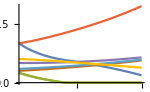
-Graphics--Graphics-

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.95,"δ"->0.85,"k"->10|>];ps=PowerStructure[{2.,0.5,0.5,2.,1.,0.6,0.7,1.2}/2,NormalizeTernaryT[({{0, -1, -1, -1, 0, 0, 0, 1}, {-1, 0, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}}) ]];
SpacedRow[{ShowPowerStructure[ps,<|"size"->{120,100}|>],SizePlot[SimulateLawOfMotion[ps]]},50]
```

#### Size plot grid

```mathematica
SetParameters[<|"β"->1.2,"μ"->1.4,"λ"->1,"ρ"->0.7,"δ"->0.8|>];Grid[Partition[Table[SizePlotQuiet[SimulateLawOfMotion[RandomTernaryPowerStructure[5,8,.2]]],12],3]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

#### Size plot 2

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.85|>];ps=PowerStructure[{.7,1,.82},NormalizeTernaryT[({{0, 1, -1}, {1, 0, 0}, {-1, 0, 0}})]];
SpacedRow[{ShowPowerStructure[ps,<|"circular"->True,"size"->{70,70}|>],SizePlotQuiet[SimulateLawOfMotion[ps]]},50]
```

-Graphics--Graphics-

#### Size plot 3

```mathematica
SetParameters[<|"β"->1.5,"μ"->2,"λ"->1,"ρ"->0.9,"δ"->0.3|>];ps=PowerStructure[{1,1},NormalizeTernaryT[({{0, 0}, {-1, 0}})]];
reel = Part[Map[ShowPowerStructure[#,<|"circular"->True,"ternary"->False,"size"->{65,40}|>]&,SimulateLawOfMotion[ps]],{1,2,3}];
SpacedRow[{SpacedRow[MapIndexed[AddCaption[#,"t = "<>ToString[First[#2]]]&,reel],25],SizePlotQuiet[SimulateLawOfMotion[ps]]},50]
```

-Graphics-
t = 1-Graphics-
t = 2-Graphics-
t = 3-Graphics-

#### Math 1

#### Math 2

#### Size plot 4

```mathematica
SetParameters[<|"β"->1.5,"μ"->2,"λ"->1,"ρ"->0.94,"δ"->0.3|>];ps=PowerStructure[{1,.7},NormalizeTernaryT[({{0, -1}, {-1, 0}})]];
reel = Part[Map[ShowPowerStructure[#,<|"circular"->True,"ternary"->False,"size"->{65,40}|>]&,SimulateLawOfMotion[ps]],{1,2,3}];
SpacedRow[{SpacedRow[MapIndexed[AddCaption[#,"t = "<>ToString[First[#2]]]&,reel],25],SizePlotQuiet[SimulateLawOfMotion[ps]]},50]
```

-Graphics-
t = 1-Graphics-
t = 2-Graphics-
t = 3-Graphics-

#### Math 3

#### Math 4

#### Math 5

#### T and M

```mathematica
M[T_]:=Table[Which[i==j,λ,T[[i,j]]≥ 0,β,True,μ],{i,Length[T]},{j,Length[T]}];SetParameters[<|"β"->2,"μ"->3,"λ"->.99,"ρ"->0.9,"δ"->0.3|>];
β=2;μ=3;λ=.99;
T=RandomTernaryT[5,4,.4];
Row[{"T =",Pretty[T] ,"    ","M =",Pretty[M[T]]}]
```

T =(0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 1
0 | -1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)    M =(0.99 | 2. | 2. | 2. | 2.
2. | 0.99 | 3. | 2. | 2.
2. | 3. | 0.99 | 2. | 2.
2. | 2. | 2. | 0.99 | 2.
2. | 2. | 2. | 2. | 0.99)

## Physical Distance

## Competition for Scarce Resources

#### Resource PS 1

```mathematica
Show[Graph[{1<->2,3->1,4->2,1<->5,6<->2,7<->2,8->1},
VertexSize -> MapIndexed[First[#2]-> #/3&,RandomReal[{.3,1},8]],
VertexStyle->{3->Purple,4->Purple,8->Purple},
EdgeStyle->{Black,1<->2->Dashed},
PerformanceGoal->"Quality"],ImageSize->Small]
```

-Graphics-

#### Possession matrix

```mathematica
Row[{
"P =",MatrixForm[{{Style[1,Background->Orange],0,0,Style[1,Background->Orange]},{0,1,0,0},{0,0,1,0}}]
}]
```

P =(1 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

#### Contention matrix

```mathematica
Row[{"C =",MatrixForm[{{1,0,0,0},{0,Style[1,Background->Orange],0,1},{0,Style[1,Background->Orange],1,0}}]}]
```

C =(1 | 0 | 0 | 0
0 | 1 | 0 | 1
0 | 1 | 1 | 0)

#### Resource PS pretty

```mathematica
Pretty[<|"s"->{.8,1,.7},"T"->({{0, 1, -1}, {1, 0, 0}, {-1, 0, 0}}),"r"->{0.03,0.11},"P"->({{1, 0}, {0, 1}, {0, 0}}),"C"->({{1, 0}, {1, 0}, {0, 0}})|>]
```

<|s→(0.8
1.
0.7),T→(0 | 1 | -1
1 | 0 | 0
-1 | 0 | 0),r→(0.03
0.11),P→(1 | 0
0 | 1
0 | 0),C→(1 | 0
1 | 0
0 | 0)|>

#### UpdateP

```mathematica
Row[{
"P =",MatrixForm[{{Style[1,Background->Orange],0,0,Style[1,Background->Green]},{0,1,0,0},{0,0,1,0}}],"   ",
"C =",MatrixForm[{{Style[1,Background->Orange],0,0,0},{0,1,0,Style[1,Background->Green]},{0,1,1,0}}],"   ",
"UpdateP[P,C]=", MatrixForm[{{Style[1,Background->Orange],0,0,0},{0,1,0,Style[1,Background->Green]},{0,0,1,0}}]
}]
```

P =(1 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0)   C =(1 | 0 | 0 | 0
0 | 1 | 0 | 1
0 | 1 | 1 | 0)   UpdateP[P,C]=(1 | 0 | 0 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 0)